## Plot Liemohn and Khazanov [1998] kappa curves

#### Somehow the derived relationship doesn’t work for integer κ … Also doesn’t match Maxwellian! Needs to be beefed up

```mathematica
densFacK[phiBar_,κ_,RB_]:=1/(phiBar^2 Gamma[κ+5/2](2 κ-3)^(3/2))√(1/(2π)) Gamma[κ+1] ( phiBar (RB-1) (κ-3/2)^2 (2 κ+5)-phiBar^2(κ-3/2) (4 κ^2+6 κ-1)+(RB-1)^2(κ-3/2)^3(1-(phiBar/((RB-1)(κ-3/2))+1)^3 Hypergeometric2F1[1,κ+1,-1/2,-(2 phiBar)/((RB-1) (2 κ-3))]))+ Csc[κ π]/2 (1/phiBar^(1/2)(phiBar/(κ-3/2)-1)^(-κ+1/2)+(4 √(2 π) Hypergeometric2F1Regularized[-1/2,1,-κ+1,(2 κ-3)/(2 phiBar)])/((2 κ-3)^(3/2)Gamma[κ-3/2]))
```

```mathematica
densFacK[phiBar_,κ_,RB_]:=1/(2 (-3+2 κ)^(3/2))((κ Gamma[κ] ((-1+RB) (-3+2 κ) (-(-1+RB)^2 (3-2 κ)^2-2 phiBar (-1+RB) (-3+2 κ) (5+2 κ)+4 phiBar^2 (-1+6 κ+4 κ^2))+(2 phiBar+(-1+RB) (-3+2 κ))^3 Hypergeometric2F1[1,1+κ,-1/2,(2 phiBar)/((-1+RB) (3-2 κ))]))/(4 phiBar^2 √(2 π) (-1+RB) Gamma[5/2+κ])+Csc[π κ] (√((3+2 phiBar-2 κ)/phiBar) (-3+2 κ) (-1+(2 phiBar)/(-3+2 κ))^-κ+(4 √(2 π) Hypergeometric2F1Regularized[-1/2,1,1-κ,(-3+2 κ)/(2 phiBar)])/Gamma[-3/2+κ]))
```

Original, unsimplified version

```mathematica
densFacK[phiBar_,κ_,RB_]:=1/(2 √phiBar (-3+2 κ)^(5/2))(phiBar (3+2 phiBar-2 κ)^-κ √((3+2 phiBar-2 κ)/phiBar) (-3+2 κ)^(2+κ) Csc[π κ]+1/(phiBar Gamma[-3/2+κ])2 √(2/π) (1/((-1+RB) (3+2 κ) (-1+4 κ^2))Gamma[1+κ] ((-1+RB) (-3+2 κ) ((-1+RB)^2 (3-2 κ)^2+2 phiBar (-1+RB) (-3+2 κ) (5+2 κ)-4 phiBar^2 (-1+6 κ+4 κ^2))-(2 phiBar+(-1+RB) (-3+2 κ))^3 Hypergeometric2F1[1,1+κ,-1/2,(2 phiBar)/((-1+RB) (3-2 κ))])+2 phiBar^2 π (-3+2 κ) Csc[π κ] Hypergeometric2F1Regularized[-1/2,1,1-κ,(-3+2 κ)/(2 phiBar)]))
```

### The Maxwellian relation, for reference Load package

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
```

```mathematica
dPhi=941;T=110;
```

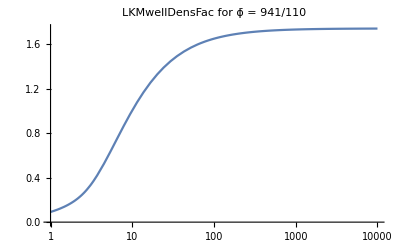

```mathematica
LogLinearPlot[LKMwellDensFac[dPhi/T,RB],{RB,1,10000},PlotLabel->"LKMwellDensFac for ϕ̄ = 941/110"]
```

#### Some plot options

```mathematica
colors={Black,Gray,Orange,Red,Brown,Green,Purple};
kappas = {1.55,1.6,1.8,2.1,4.3,9.75};
```

```mathematica
placeList={Above,Above,Above,Above,Above,Above,Above};
nDigs={3,3,3,3,3,3};
kapStrVals=Table[NumberForm[kappas[[k]],nDigs[[k]]],{k,1,6}];
kappaLabels=Table[StringForm["κ = `1`",kapStrVals[[k]]],{k,1,6}];
nDigitsdPhi=3;nDigitsTm=3;
RBMin=1;RBMax=10000;
```

```mathematica
showers={1,2,3,4,5,6};
(*showers={1};*)
```

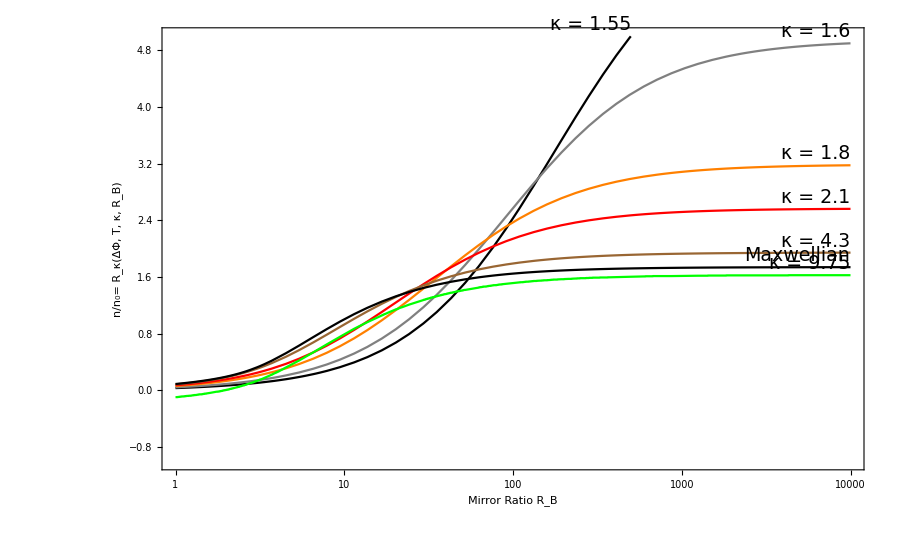

```mathematica
Show[Table[LogLinearPlot[densFacK[dPhi/T,kappas[[k]],RB],{RB,RBMin,RBMax},PlotRange->{{RBMin,RBMax},{-1,5}},PlotStyle->colors[[k]],Frame->True,PlotLabels ->Placed[kappaLabels[[k]] ,placeList[[k]]],LabelStyle->(FontSize->19),FrameLabel->{{StringForm["n/n_0= R_κ(ΔΦ, T, κ, R_B)"],""},{StringForm["Mirror Ratio R_B"],StringForm["ΔΦ = `1` V; T_m= `2` eV; ϕ̄= `3`",NumberForm[dPhi,nDigitsdPhi],NumberForm[T,nDigitsTm],NumberForm[N[dPhi/T],{3,1}]]}},ImageSize->900],{k,showers}],LogLinearPlot[LKMwellDensFac[dPhi/T,RB],{RB,RBMin,RBMax},PlotRange->{{RBMin,RBMax},{-1,5}},PlotStyle->Black,Frame->True,FrameStyle->Black,PlotLabels ->Placed[StringForm["Maxwellian"] ,Above],LabelStyle->(FontSize->19),FrameLabel->{{StringForm["n/n_0= R_κ(ΔΦ, T, κ, R_B)"],""},{StringForm["Mirror Ratio R_B"],StringForm["ΔΦ = `1` V; T_m= `2` eV; ϕ̄= `3`",NumberForm[dPhi,nDigitsdPhi],NumberForm[T,nDigitsTm],NumberForm[N[dPhi/T],{3,1}]]}},ImageSize->900]]
```

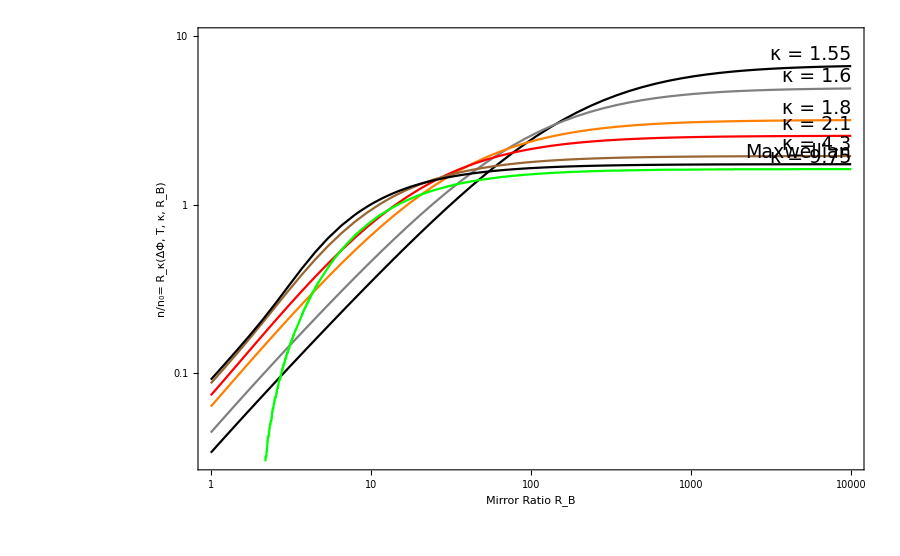

```mathematica
Show[Table[LogLogPlot[densFacK[dPhi/T,kappas[[k]],RB],{RB,RBMin,RBMax},PlotRange->{{RBMin,RBMax},{.03,10}},PlotStyle->colors[[k]],Frame->True,PlotLabels ->Placed[kappaLabels[[k]] ,placeList[[k]]],LabelStyle->(FontSize->19),FrameLabel->{{StringForm["n/n_0= R_κ(ΔΦ, T, κ, R_B)"],""},{StringForm["Mirror Ratio R_B"],StringForm["ΔΦ = `1` V; T_m= `2` eV; ϕ̄= `3`",NumberForm[dPhi,nDigitsdPhi],NumberForm[T,nDigitsTm],NumberForm[N[dPhi/T],{3,1}]]}},ImageSize->900],{k,showers}],LogLogPlot[LKMwellDensFac[dPhi/T,RB],{RB,RBMin,RBMax},PlotRange->{{RBMin,RBMax},{.03,10}},PlotStyle->Black,Frame->True,FrameStyle->Black,PlotLabels ->Placed[StringForm["Maxwellian"] ,Above],LabelStyle->(FontSize->19),FrameLabel->{{StringForm["n/n_0= R_κ(ΔΦ, T, κ, R_B)"],""},{StringForm["Mirror Ratio R_B"],StringForm["ΔΦ = `1` V; T_m= `2` eV; ϕ̄= `3`",NumberForm[dPhi,nDigitsdPhi],NumberForm[T,nDigitsTm],NumberForm[N[dPhi/T],{3,1}]]}},ImageSize->900]]
```